```mathematica
portfolio={"BTC","ETH"};
data =FinancialData[#, {{2010},{2020}}]&/@portfolio;
data = TimeSeriesResample[{data[[1]], data[[2]]},"Intersection"];
```

```mathematica
returns = Differences@*Log/@data[[All, All, 2]];
```

```mathematica
btcSD = StandardDeviation[returns[[1]]] ;
ethSD = StandardDeviation[returns[[2]]];
```

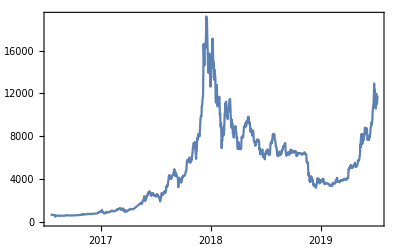

```mathematica
data[[1]]//DateListPlot
```

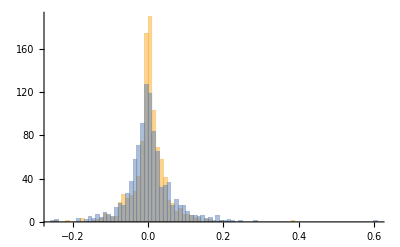

```mathematica
Histogram[returns, PlotRange -> All]
```

```mathematica
(* returns = Differences[#]&/@Table[Log[10, Part[#,2]]&/@x,{x,data}] *)
```

```mathematica
correlated =Correlation[returns[[1]], returns[[2]]];
```

```mathematica
optimize[btcreturn_, ethreturn_, btcvolatility_, ethvolatility_, correlation_] := NMaximize[{Sqrt[252](weight*btcreturn+(1-weight)*ethreturn)/Sqrt[btcvolatility^2*weight^2 + ethvolatility^2*(1-weight)^2 + (2*correlation*btcvolatility*ethvolatility)*weight*(1-weight)], 1≥ weight ≥ 0}, weight]
```

```mathematica
optimize[Mean[returns[[1]]], Mean[returns[[2]]], btcSD, ethSD, correlated]
```

{1.22866,{weight→0.629921}}

```mathematica
Manipulate[Sqrt[252.](weight*btcreturn+(1-weight)*ethreturn)/Sqrt[btcvolatility^2*weight^2 + ethvolatility^2*(1-weight)^2 + (2*correlation*btcvolatility*ethvolatility)*weight*(1-weight)] ->  (optimize[Mean[btcreturn[[1]]], Mean[returns[[2]]], btcSD, ethSD, correlated]),{weight, 0, 1}, {{btcreturn, Mean[returns[[1]]]}, 0, 0.02}, {{ethreturn, returns[[2]]//Mean}, 0, 0.02}, {{btcvolatility, btcSD}, 0, 1}, {{ethvolatility, ethSD}, 0, 1}, {{correlation, correlated}, 0, 1}]
```